```mathematica
(*Using Zhu, Xiong paper*)
(* Distance between nuclei*)

(**)

(* Solve the separated equation in 2D *)
(* L equation and coefficients *)
σ[r_]:=r/p-1/2;
α[n_]:=(n+1)(n+1/2);
β[n_,r_]:=2 n^2+(4p-2σ[r])n-A +p^2-2p σ[r]-σ[r]/2;
γ[n_,r_]:=(n-1)(n-2σ[r]-1/2)+σ[r](σ[r]-1/2);

(* Create a continued fraction equation for the coefficients of L equation *)

lCoeff2[n_,r_]:=β[0,r]/α[0]+Simplify[ContinuedFractionK[-α[i-1]γ[i,r],β[i,r],{i,1,n}]] ;

(* M equation and coefficients *)

w=-A +p^2/2;      q= -p^2/4;
v[n_]:=(w-n^2)/q;
(* Evaluate as a continued fraction *)
mCoeffV0[n_]:=v[0]+2Simplify[ContinuedFractionK[-1,v[2i],{i,1,n}]];

mCoeffV1[n_]:=v[1]-1+Simplify[ContinuedFractionK[-1,v[2i+1],{i,1,n}]];

(* Compute the eigenvalue, i.e. the energy for the single value of R .
R - internuclear separation *)
(* Parameters:
n: Depth of the continued fraction,
 R: Internuclear distance,
 gerade: flag indicating whether we are calculating gerade or ungerade states
output:
R , electron energy, total energy, separation constant, and p value 
*)
energySingleR[n_,R_, gerade_]:=
Module[{asAndps,pe,energy,aa},
(*Now find p and A *)
If[gerade==1, 
asAndps= NSolve[{lCoeff2[n,R]==0,
mCoeffV0[n]==0},{A,p},Reals],
asAndps= NSolve[{lCoeff2[n,R]==0,
mCoeffV1[n]==0},{A,p},Reals]];
aa=Sort[asAndps[[All,1,2]], Greater][[1]];
pe=Sort[asAndps[[All,2,2]], Greater][[1]];
energy = (-2)/R^2 pe^2;
{R,energy, energy + 1/R,aa,pe}
]
allRs = Table[0.2+i*0.1,{i,0,9}];
allRs = Join[allRs, Table[1+.5*i,{i,1,8}]];
allRs = Join[allRs, Table[5+i,{i,1,45}]];

energiesGerade1S = Map[energySingleR[9,#1,1] &, allRs];
energiesUngerade1S = Map[energySingleR[9,#1,2] &, allRs];
Prepend[energiesGerade1S, {"R", "E", "E+1/r", "A", "p"}]  ;
Prepend[energiesUngerade1S, {"R", "E", "E+1/r", "A", "p"}]  ;

energiesGerade1S //MatrixForm
energiesUngerade1S//MatrixForm

grid=Transpose@{energiesGerade1S[[All,1]],energiesGerade1S[[All,3]],energiesUngerade1S[[All,3]],energiesGerade1S[[All,3]]- energiesUngerade1S[[All,3]]};
grid // MatrixForm
```

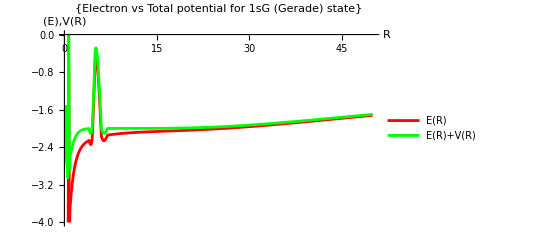

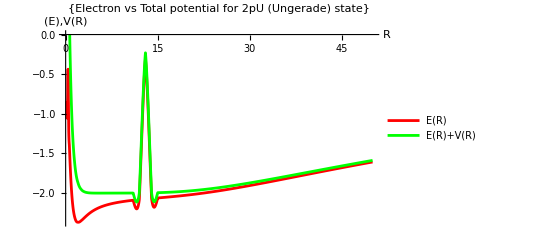

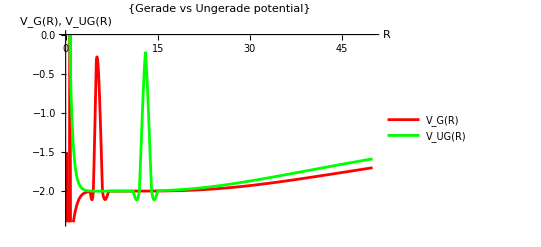

```mathematica
(* Export as above: A, p are constants *)
(* Export to a file so that it can be loaded by other programs *)
Export["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV2.mx",energiesGerade1S, "mx"];
Prepend[energiesUngerade1S, {"R", "E","E+1/r", "A", "p"}];
Export["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV2.mx",energiesUngerade1S, "mx"];

eG = Interpolation[Transpose[{energiesGerade1S[[All,1]],energiesGerade1S[[All,2]]}]];
eGTotal = Interpolation[Transpose[{energiesGerade1S[[All,1]],energiesGerade1S[[All,3]]}]];


Plot[{eG[x],eGTotal[x]},{x,.2,50}, PlotStyle->{Red,Green}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 1sG (Gerade) state"},
PlotRange->{0,-4},PlotLegends->{"E(R)","E(R)+V(R)","egFar"}]


eU = Interpolation[Transpose[{energiesUngerade1S[[All,1]],energiesUngerade1S[[All,2]]}], InterpolationOrder->3];
eUTotal = Interpolation[Transpose[{energiesUngerade1S[[All,1]],energiesUngerade1S[[All,3]]}], InterpolationOrder->3];

Plot[{eU[x],eUTotal[x]},{x,0.2,50}, PlotStyle->{Red,Green}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 2pU (Ungerade) state"}, PlotLegends->{"E(R)","E(R)+V(R)"}]

Plot[{eGTotal[x],eUTotal[x]},{x,0.2,50}, PlotStyle->{Red,Green}, AxesLabel->{"R", "V_G(R), V_UG(R)"}, AxesOrigin->{0,0},PlotLabel->{"Gerade vs Ungerade potential"}, PlotLegends->{"V_G(R)","V_UG(R)"}]
```